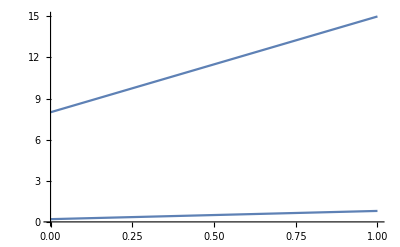

```mathematica
Plot[(1-n)(a+b)+n(a*b)//ReIm,{n,0,1}]
```

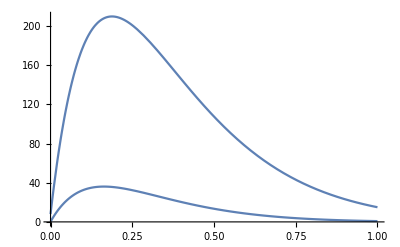

```mathematica
LinExp[x_,n_]:=(1-n)x+n Exp[x];
LinLog[x_,n_]:=(1-n)x+n Log[x];
Plot[LinExp[LinLog[a,n]+LinLog[b,n],n]//ReIm,{n,0,1}]
```

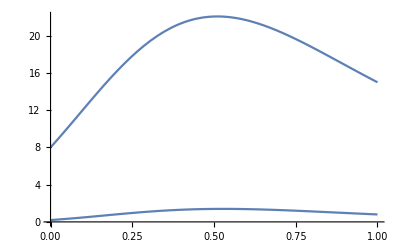

```mathematica
LinExpP[x_,n_]:=x^(1-n) Exp[x]^n;
LinLogP[x_,n_]:=x^(1-n)Log[x]^n;
Plot[LinExpP[LinLogP[a,n]+LinLogP[b,n],n]//ReIm,{n,0,1}]
```